```mathematica
Quit[]
```

```mathematica
Get["DdimPackage.wl"]
```

Get::noopen: Cannot open YoungSymm`.

Needs::nocont: Context YoungSymm` was not created when Needs was evaluated.

```mathematica
Get["/Users/gangchen/Documents/GitHub/WaveFormOneLoopQM/Amplitude/1-loop_HEFT_amplitude_result.wl"]
```

parametrise picks a frame (here I am considering the ϵ_k^+ helicity polarisation):

## Plus Polarisation

```mathematica
ClearAll[parametrise]
parametrise[exp_]:=ReplaceRepeated[exp,{DotProduct[Momentum[x_],Momentum[y_]]:>x.DiagonalMatrix[{1,-1,-1,-1}].y,DotProduct[EpsilonPol[k],Momentum[y_]]:>ϵk.DiagonalMatrix[{1,-1,-1,-1}].y}]/.{u1->{1,0,0,0},u2->{γ,V γ,0,0},k->ω{1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},b->{0,0,B,0},v->{0,0,0,4 B √(-1+γ^2)},ϵk->{0,(Cos[θ] Cos[ϕ]-I Sin[ϕ]),(Cos[θ] Sin[ϕ]+I Cos[ϕ]),-Sin[θ]}}
```

```mathematica
(*{k.DiagonalMatrix[{1,-1,-1,-1}].{ϵk0,ϵk1,ϵk2,ϵk3},{ϵk0,ϵk1,ϵk2,ϵk3}.DiagonalMatrix[{1,-1,-1,-1}].{ϵk0,ϵk1,ϵk2,ϵk3}}/.{u1->{1,0,0,0},u2->{γ,γ v,0,0},k->ω{1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},b->{0,0,b,0},v->{0,0,0,4 b Sqrt[γ^2-1]}}
Solve[%==0,{ϵk0,ϵk1}][[1]]
%/.θ->0/.{ϵk3->0,ϵk2->1}*)
```

```mathematica
g0=2;
```

```mathematica
amp1=-I amp5TreeLevel/. replaceTree;
```

```mathematica
(*amp5=amp5m13m22/. replaceDivergences/. amp5TreeLevel->0/. replacer[]/. replacelq[]/. replacely[]/. replacelw2[]/.replaceTriangleIntegrals/.replacec1/.replacec2;*)
```

```mathematica
amp1//.{F1->FTrace[Momentum[q1],{FieldStr[k]},Momentum[v1]],F2->FTrace[Momentum[q2],{FieldStr[k]},Momentum[v2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
(*%//Reduce`FreeVariables*)
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->g0(*ω->3*)};
amp1=%+ReplaceAll[%,zv->-zv]//Expand[#,1]&;
(*%//Series[#,zv->Infinity]&
%%//Series[#,{zb,Infinity,0}]&*)
```

```mathematica
amp1//Length
```

2

### Continue

```mathematica
Monitor[amp1=Sum[amp1[[ii]]//Simplify,{ii,Length@amp1}];,ii]
```

```mathematica
amp10=ω^2amp1/.{zb->ω zb,zv->ω zv}//Simplify
```

(3 √3 (36 (11+28 ⅈ √3) zb^4-63 ⅈ √2 (-3 ⅈ+4 √3) zb^5+12 zb^2 (76+128 ⅈ √3+(3+84 ⅈ √3) zv^2)-6 ⅈ √2 zb^3 (-111 ⅈ+212 √3+21 (-3 ⅈ+4 √3) zv^2)-8 (-16+12 (7-2 ⅈ √3) zv^2+45 zv^4)+3 √2 zb (-208-192 ⅈ √3+(366-88 ⅈ √3) zv^2+(-63-84 ⅈ √3) zv^4)))/(16 (4+3 zb^2+3 zv^2) (4-3 √2 zb+3 zb^2-3 √2 zv+3 zv^2) (4-3 √2 zb+3 zb^2+3 √2 zv+3 zv^2))

```mathematica
amp1list=List@@(amp1//Apart[#,zb]&//Expand);
```

```mathematica
amp1list0=List@@(amp10//Apart[#,zb]&//Expand);
```

```mathematica
(List@@@(Denominator/@amp1list))//Flatten//Union
```

{2,4,8,√2,2+3 zv^2,4+3 zb^2+3 zv^2,4-3 √2 zb+3 zb^2-3 √2 zv+3 zv^2,4-3 √2 zb+3 zb^2+3 √2 zv+3 zv^2}

```mathematica
NIntegrate[Exp[-I zb ω-0.0001 Abs[zb ]](Total@amp1list0)/.ω->0.1,{zb,-Infinity,Infinity},{zv,0,Infinity},Method->"LocalAdaptive"]
```

-256.972+100.641 ⅈ

```mathematica
NIntegrate[Exp[-I zb -0.001 Abs[zb ]](Total@amp1list)/.ω->0.1,{zb,-Infinity,Infinity},{zv,0,Infinity},Method->"LocalAdaptive"]
```

-256.972+100.641 ⅈ

```mathematica
numList=ParallelTable[NIntegrate[Exp[-I zb ω-0.001 Abs[zb]](Total@amp1list)/.ω->ii,{zb,-Infinity,Infinity},{zv,0,Infinity},Method->"LocalAdaptive"],{ii,0.1,25,0.1}]
```

$Aborted

## Minus Polarisation

```mathematica
ClearAll[parametrise]
parametrise[exp_]:=ReplaceRepeated[exp,{DotProduct[Momentum[x_],Momentum[y_]]:>x.DiagonalMatrix[{1,-1,-1,-1}].y,DotProduct[EpsilonPol[k],Momentum[y_]]:>ϵk.DiagonalMatrix[{1,-1,-1,-1}].y}]/.{u1->{1,0,0,0},u2->{γ,V γ,0,0},k->ω{1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},b->{0,0,B,0},v->{0,0,0,4 B √(-1+γ^2)},ϵk->{0,(Cos[θ] Cos[ϕ]+I Sin[ϕ]),(Cos[θ] Sin[ϕ]-I Cos[ϕ]),-Sin[θ]}}
```

```mathematica
amp1Neg=-I amp5TreeLevel/. replaceTree;
```

```mathematica
amp1Neg//.{F1->FTrace[Momentum[q1],{FieldStr[k]},Momentum[v1]],F2->FTrace[Momentum[q2],{FieldStr[k]},Momentum[v2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
(*%//Reduce`FreeVariables*)
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->g0(*ω->3*)};
amp1Neg=%+ReplaceAll[%,zv->-zv]//Expand[#,1]&;
(*%//Series[#,zv->Infinity]&
%%//Series[#,{zb,Infinity,0}]&*)
```

```mathematica
(amp1-Conjugate[amp1Neg])/.Thread[{zv,zb,ω}->RandomInteger[{1,100},3]]//Simplify
```

0

```mathematica
(*amp1//Length*)
```

```mathematica
(*amp1*)
```

### Continue

```mathematica
(*Monitor[amp1=Sum[amp1[[ii]]//Simplify,{ii,Length@amp1}];,ii]*)
```

```mathematica
(*amp1//Simplify*)
```

```mathematica
(*amp1list=List@@(amp1//Apart[#,zb]&//Expand);*)
```

## PlotPP

```mathematica
$interval=0.1;
$finiteSize=12;
```

```mathematica
(*numList=Table[NIntegrate[amp10PP/.ω->ii,{zv,0,∞}],{ii,$interval,$finiteSize,$interval}];*)
```

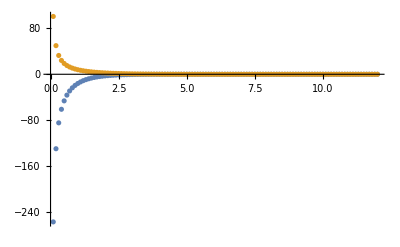

```mathematica
wlist=Table[ii,{ii,$interval,$finiteSize,$interval}];
num=Table[numList[[ii]] ,{ii,Length@wlist}];
wfFRe=Transpose[{wlist,Re/@num}];
wfFIm=Transpose[{wlist,Im/@num}];
ListPlot[{wfFRe,wfFIm},PlotRange->All]
```

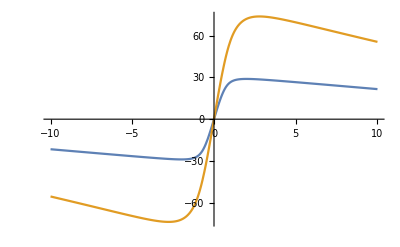

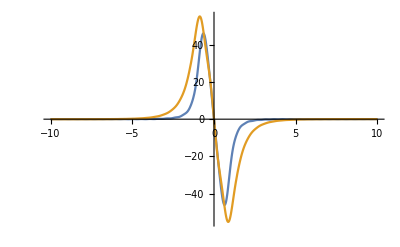

```mathematica
exp1=Table[Exp[-I ω t]/.ω->i,{i,wlist}];
exp2=Table[Exp[I ω t]/.ω->i,{i,wlist}];
Total[0.1*(exp1.num-exp2.num)];
Plot[{Re[%],Im[%]},{t,-10,10},PlotRange->All]
D[%%,{t,2}];
Plot[{Re[%],Im[%]},{t,-10,10},PlotRange->All]
```